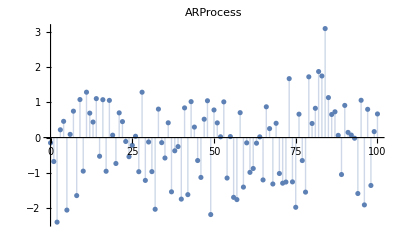
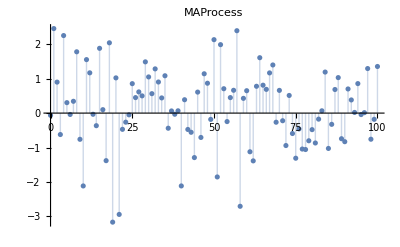

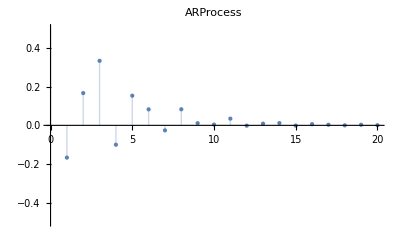
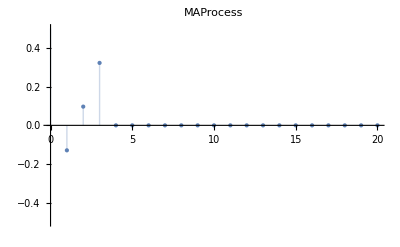

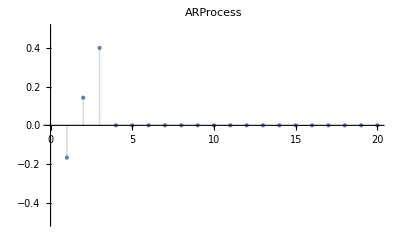
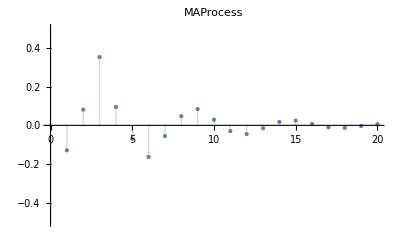

```mathematica
ar=ARProcess[{-.2,.2,.4},1];
ma=MAProcess[{-.2,.2,.4},1];
ListPlot[RandomFunction[#,{0,100}],Filling->0,PlotLabel->Head[#]]&/@{ar,ma}
ListPlot[CorrelationFunction[#,{20}],PlotLabel->Head[#],Filling->0,PlotRange->{-.5,.5},PlotStyle->PointSize[Medium]]&/@{ar,ma}
ListPlot[PartialCorrelationFunction[#,{20}],PlotLabel->Head[#],Filling->0,PlotRange->{-.5,.5},PlotStyle->PointSize[Medium]]&/@{ar,ma}
```